```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/jure/Documents/sissa/simulations/molecular_simulation

```mathematica
energy1=Import["/home/jure/Documents/sissa/simulations/molecular_simulation/data/energy_box_size_10.000000_num_particle100_temperature_1.000000.dat"];
energy1[[1]]
```

{-83.0282,-438.309}

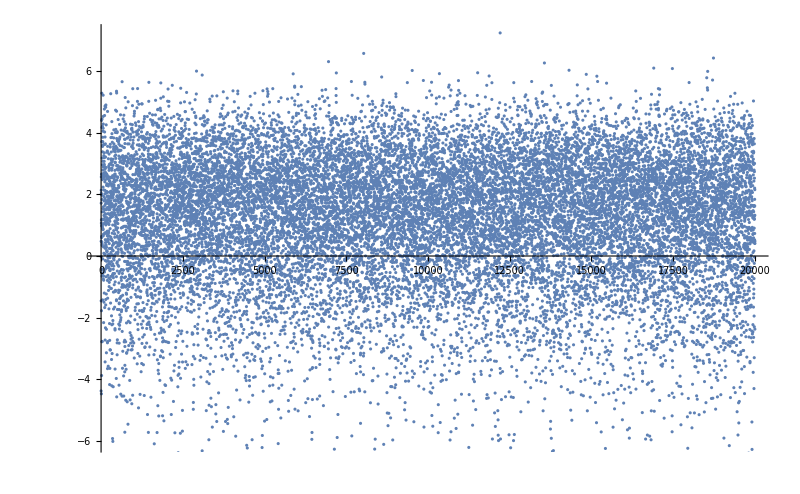

```mathematica
ListPlot[energy1[[All,2]]/100, ImageSize->800]
```

```mathematica
(energy1[[All,1]]//StandardDeviation)/100
```

0.11933

```mathematica
energy2=Import["/home/jure/Documents/sissa/simulations/molecular_simulation/data/energy_box_size_99.000000_num_particle100_temperature_1.000000.dat"];
```

Import::nffil: File not found during Import.

```mathematica
Clear[cv]
cv[size_]:=Block[{data,str1,str2, str, heat, temp},
str1="/home/jure/Documents/sissa/simulations/molecular_simulation/data/energy_box_size_";
str2="_num_particle100_temperature_1.000000.dat";
str=StringJoin[str1,ToString[NumberForm[size*1.0,{∞,6}]],str2];
data=Import[str];
heat=(3/2*NumParticles+temp^2*Variance[data[[All, 1]]])/NumParticles;
Return[heat];
]
```

```mathematica
cv[5]
```

((3 NumParticles)/2+88.785 temp^2)/NumParticles

```mathematica
temp=1;
NumParticles=100
SpecHeat=Table[{100/i^3,cv[i*0.5]},{i,1,99}];
```

100

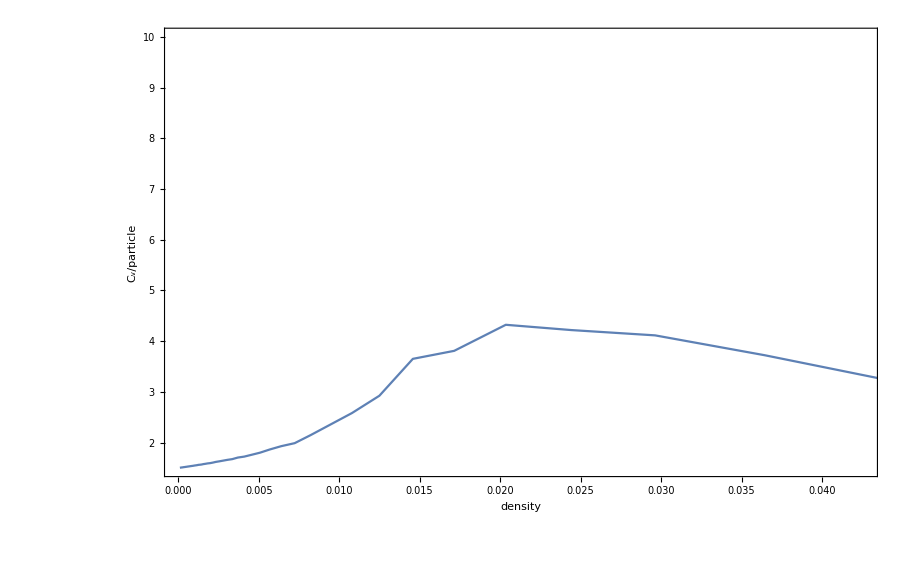

```mathematica
ListLinePlot[SpecHeat, Frame->True, FrameLabel->{Style["density", 20], Style["C_v/particle", 20]}, PlotRange->{Automatic,{1.5,10}}]
```

```mathematica
pressure[size_]:=Block[{data,str1,str2, str, kineticEnergy, temp},
str1="/home/jure/Documents/sissa/simulations/molecular_simulation/data/energy_box_size_";
str2="_num_particle100_temperature_1.000000.dat";
str=StringJoin[str1,ToString[NumberForm[size*1.0,{∞,6}]],str2];
data=Import[str];
kineticEnergy=(NumParticles*temp -1/3*Mean[data[[All, 2]]])/size^3;
Return[kineticEnergy];
]
```

```mathematica
temp=1;
NumParticles=100
t=Table[{i^3,pressure[i*0.5]},{i,1,99}];
```

100

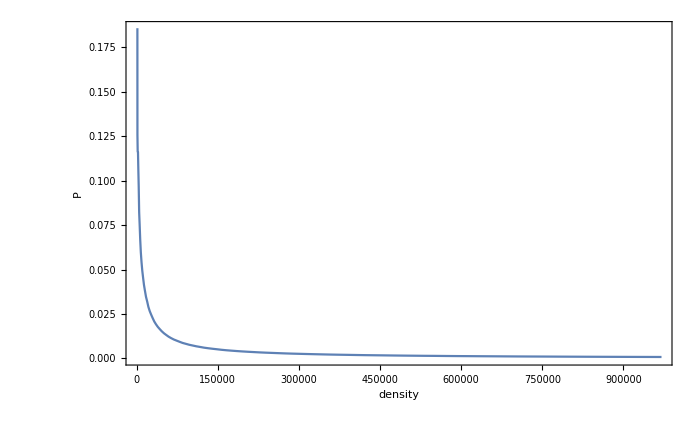

```mathematica
ListLinePlot[t, Frame->True, FrameLabel->{Style["density", 20], Style["P", 20]}, PlotRange->{Automatic,Automatic}, ImageSize->700]
```

```mathematica
Clear[cv]
cv[temp_]:=Block[{data,str1,str2, str, heat},
str1="/home/jure/Documents/sissa/simulations/molecular_simulation/data/energy_box_size_10.000000_num_particle100_temperature_";
str2=".dat";
str=StringJoin[str1,ToString[NumberForm[temp*1.0,{∞,6}]],str2];
data=Import[str];
heat=(3/2*NumParticles+temp^2*Variance[data[[All, 1]]])/NumParticles;
Return[heat];
]
```

```mathematica
temp=1;
NumParticles=100
SpecHeat=Table[{t/10,cv[t/10.0]},{t,0,99}];
```

100

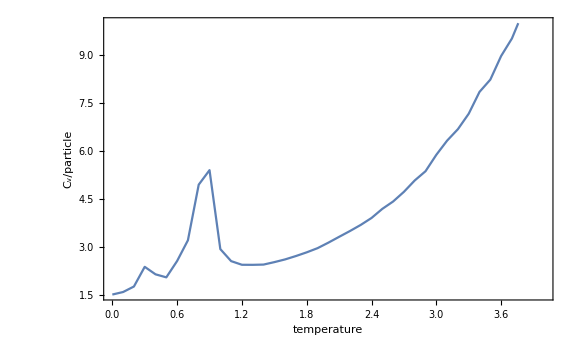

```mathematica
ListLinePlot[SpecHeat, Frame->True, FrameLabel->{Style["temperature", 20], Style["C_v/particle", 20]}, PlotRange->{{0,4},{1.5,10}}, ImageSize->Large]
```

```mathematica
pressure[temp_]:=Block[{data,str1,str2, str, kineticEnergy},
str1="/home/jure/Documents/sissa/simulations/molecular_simulation/data/energy_box_size_10.000000_num_particle100_temperature_";
str2=".dat";
str=StringJoin[str1,ToString[NumberForm[temp*1.0,{∞,6}]],str2];
data=Import[str];
kineticEnergy=(NumParticles*temp -1/3*Mean[data[[All, 2]]])/10^3;
Return[kineticEnergy];
]
```

```mathematica
temp=1;
NumParticles=100
p=Table[{t/10.0,pressure[t/10.0]},{t,0,99}];
```

100

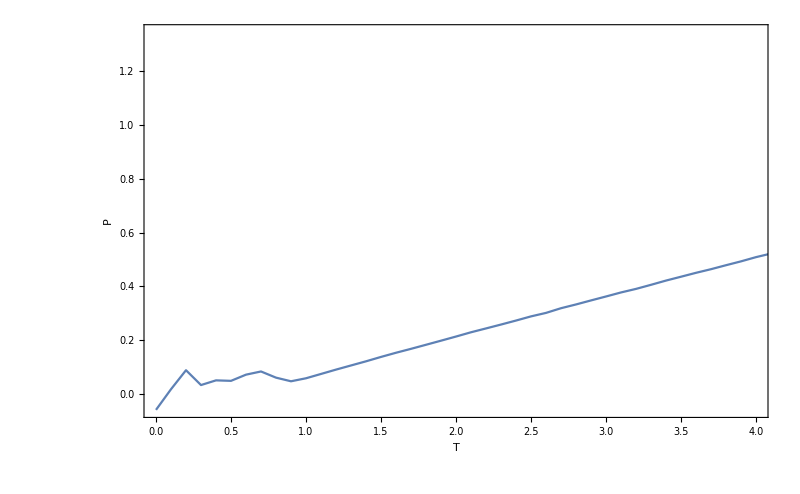

```mathematica
ListLinePlot[p, Frame->True, FrameLabel->{Style["T", 20], Style["P", 20]}, PlotRange->{{0,4},Automatic}, ImageSize->800]
```